# Generic Natario warp drive and deflector shield

## Geometric quantities

```mathematica
ClearAll[coordsU];
coordsU={t,x,y,z};

ClearAll[vU];
vU={vx[t,x,y,z],vy[t,x,y,z],vz[t,x,y,z]};

ClearAll[gUU];
gUU={
{-1,-vU[[1]],-vU[[2]],-vU[[3]]},
{-vU[[1]],1-vU[[1]]vU[[1]],-vU[[1]]vU[[2]],-vU[[1]]vU[[3]]},
{-vU[[2]],-vU[[2]]vU[[1]],1-vU[[2]]vU[[2]],-vU[[2]]vU[[3]]},
{-vU[[3]],-vU[[3]]vU[[1]],-vU[[3]]vU[[2]],1-vU[[3]]vU[[3]]}
};

gLL=FullSimplify[Inverse[gUU]];

ClearAll[nU,nL];
nU=Join[{1},vU];
nL=FullSimplify[ParallelTable[Sum[gLL[[a,b]]nU[[b]],{b,1,4}],{a,1,4}]];

ClearAll[Γ];
Γ=ParallelTable[
FullSimplify[
(1/2)*Sum[
(gUU[[i,s]])*(D[gLL[[s,j]],coordsU[[k]] ]+D[gLL[[s,k]],coordsU[[j]] ]-D[gLL[[j,k]],coordsU[[s]] ]),
{s,1,4}
]
],
{i,1,4},
{j,1,4},
{k,1,4}
] ;

ClearAll[RiemannLLLL];
RiemannLLLL=ParallelTable[
FullSimplify[
D[Γ[[i,j,l]],coordsU[[k]] ]-D[Γ[[i,j,k]],coordsU[[l]] ]+Sum[
Γ[[s,j,l]] Γ[[i,k,s]]-Γ[[s,j,k]] Γ[[i,l,s]],
{s,1,4}
]
],
{i,1,4},
{j,1,4},
{k,1,4},
{l,1,4}
];

ClearAll[RicciLL];
RicciLL=FullSimplify[ParallelTable[Sum[RiemannLLLL[[i,j,i,l]],{i,1,4}],{j,1,4},{l,1,4}] ];

ClearAll[RicciScalar];
RicciScalar=FullSimplify[Sum[gUU[[i,j]]RicciLL[[i,j]],{i,1,4},{j,1,4}] ];

ClearAll[EinsteinLL];
EinsteinLL=FullSimplify[RicciLL-(1/2)RicciScalar*gLL];
```

The Eulerian observer is a solution of the geodesic equation

```mathematica
FullSimplify[
Table[
Sum[nU[[b]](D[nL[[b]],coordsU[[1]]]-Sum[Γ[[i,b,a]]nL[[i]],{i,1,4}]),{a,1,4},{b,1,4}],{c,1,4}
]
]
```

{0,0,0,0}

```mathematica
ClearAll[EnergyDensity];
EnergyDensity=FullSimplify[1/(8π)Sum[EinsteinLL[[a,b]]*nU[[a]]nU[[b]],{a,1,4},{b,1,4}]]
```

-1/(32 π)((vy^(0,0,0,1)[t,x,y,z]+vz^(0,0,1,0)[t,x,y,z])^2-4 vy^(0,0,1,0)[t,x,y,z] vx^(0,1,0,0)[t,x,y,z]-4 vz^(0,0,0,1)[t,x,y,z] (vy^(0,0,1,0)[t,x,y,z]+vx^(0,1,0,0)[t,x,y,z])+(vx^(0,0,1,0)[t,x,y,z]+vy^(0,1,0,0)[t,x,y,z])^2+(vx^(0,0,0,1)[t,x,y,z]+vz^(0,1,0,0)[t,x,y,z])^2)

## Bubble transition functions

### Sharp transition

```mathematica
(*https://www.j-raedler.de/2010/10/smooth-transition-between-functions-with-tanh*)
(*https://en.wikipedia.org/wiki/Non-analytic_smooth_function#Smooth_transition_functions*)
ClearAll[SNAf,SNAg,SNAh];
SNAf[x_]:=Piecewise[{{Exp[-1/x],x>0},{0,x<=0}}];
SNAg[x_]:=SNAf[x]/(SNAf[x]+SNAf[1-x]);
SNAh[xa_,xb_,x_]:=SNAg[(x-xa)/(xb-xa)];

ClearAll[T];
T[a_,xa_,b_,xb_,x_]:=b*SNAh[xa,xb,x]+(1-SNAh[xa,xb,x])a;

ClearAll[TopHat];
TopHat[σ_,R_,x_]:=T[0,-(R+σ),1,-R,x]T[1,R,0,R+σ,x];
```

```mathematica
ClearAll[th];
th=FullSimplify[TopHat[σ,R,x],{σ∈Reals,R∈Reals,x∈Reals,σ>0,R>0,x>=0}]
```

Piecewise[{{1/(1+ⅇ^(σ (1/(R-x)+1/(R-x+σ)))), R<x&&R+σ>x}, {0, R<x}, {1, True}}]

```mathematica
ClearAll[dth];
dth=FullSimplify[Derivative[0,0,1][TopHat][σ,R,x],{σ∈Reals,R∈Reals,x∈Reals,σ>0,R>0,x>=0}]
```

Piecewise[{{-(σ (2 (R-x)^2+2 (R-x) σ+σ^2) Sech[1/2 σ (1/(R-x)+1/(R-x+σ))]^2)/(4 (R-x)^2 (R-x+σ)^2), R<x&&R+σ>x}, {0, True}}]

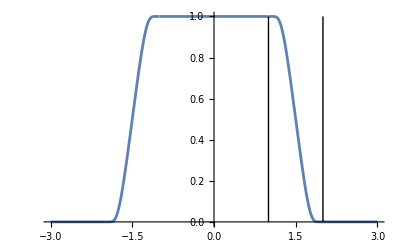

```mathematica
ClearAll[R,σ];
R=1;
σ=1;

Plot[
TopHat[σ,R,x],
{x,-3,3},
Epilog->{
Line[{{R,0},{R,1}}],
Line[{{R+σ,0},{R+σ,1}}]
}
]

ClearAll[R,σ];
```

### Alcubierre transition

```mathematica
ClearAll[AlcubierreTransition]
AlcubierreTransition[σ_,R_,r_]:=(Tanh[σ(r+R)]-Tanh[σ(r-R)])/(2Tanh[σ*R]);
```

```mathematica
ClearAll[alc,dalc];
dalc=FullSimplify[Derivative[0,0,1][AlcubierreTransition][σ,R,x],{σ∈Reals,R∈Reals,x∈Reals,σ>0,R>0,x>=0}]
```

1/2 σ Coth[R σ] (-Sech[(-R+x) σ]^2+Sech[(R+x) σ]^2)

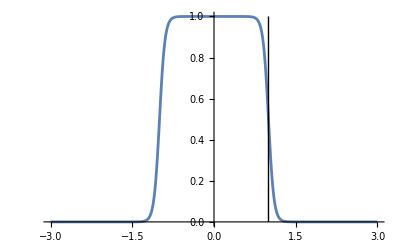

```mathematica
ClearAll[R,σ];
R=1;
σ=10;

Plot[
AlcubierreTransition[σ,R,x],
{x,-3,3},
Epilog->{
Line[{{R,0},{R,1}}]
}
]

ClearAll[R,σ];
```

### Polynomial transition

```mathematica
ClearAll[basePolyOrder,basePoly];
basePolyOrder=7;
basePoly[x_]=Sum[c[i]x^i,{i,0,basePolyOrder}];

ClearAll[coeffList];
coeffList=Table[c[i],{i,0,basePolyOrder}];

ClearAll[coeffSol];
coeffSol=Solve[
{
basePoly[xa]==a,
basePoly[xb]==b,
Derivative[1][basePoly][xa]==0,
Derivative[1][basePoly][xb]==0,
Derivative[2][basePoly][xa]==0,
Derivative[2][basePoly][xb]==0,
Derivative[3][basePoly][xa]==0,
Derivative[3][basePoly][xb]==0
},
coeffList
]//Flatten//FullSimplify;

ClearAll[TPoly]
TPoly[a_,xa_,b_,xb_,x_]=Piecewise[
{
{a,x<xa},
{b,x>xb},
{(basePoly[x]//.coeffSol),True}
}];

ClearAll[TopHatPoly];
TopHatPoly[σ_,R_,x_]=TPoly[0,-(R+σ),1,-R,x]TPoly[1,R,0,R+σ,x];
```

## Particle Hamiltonian

```mathematica
ClearAll[pL];
pL={pt,px,py,pz};

ClearAll[H];
H=FullSimplify[1/2Sum[gUU[[a,b]]pL[[a]]pL[[b]],{a,1,4},{b,1,4}]];

ClearAll[dHdpL];
dHdpL=FullSimplify[Table[D[H,pL[[i]]],{i,1,4}]];

ClearAll[dHdqU];
dHdqU=FullSimplify[Table[D[H,coordsU[[i]]],{i,1,4}]];

ClearAll[NormCons];
NormCons=Collect[(H-δ/2),pt,FullSimplify];
```

## Code strings

### Propper formating of Power

```mathematica
Unprotect[Power];
Format[Power[E,a_],CForm]:=(exp[a]);
Format[Power[a_,1/2],CForm]:=(sqrt[a]);
Format[Power[a_,-1/2],CForm]:=(1/sqrt[a]);
Format[Power[a_,3/2],CForm]:=(a*sqrt[a]);
Format[Power[a_,b_],CForm]:=(pow[a,b]);
Format[Power[a_,2],CForm]:=(HoldForm[a*a]);
Format[Power[a_,-1],CForm]:=(HoldForm[1/(a)]);
Format[Power[a_,-2],CForm]:=(HoldForm[1/((a)*(a))]);
Protect[Power];
```

### Variable replacement rules

```mathematica
ClearAll[vRules];
vRules={
D[vx[t,x,y,z],t]->dvxdt,
D[vx[t,x,y,z],x]->dvxdx,
D[vx[t,x,y,z],y]->dvxdy,
D[vx[t,x,y,z],z]->dvxdz,

D[vy[t,x,y,z],t]->dvydt,
D[vy[t,x,y,z],x]->dvydx,
D[vy[t,x,y,z],y]->dvydy,
D[vy[t,x,y,z],z]->dvydz,

D[vz[t,x,y,z],t]->dvzdt,
D[vz[t,x,y,z],x]->dvzdx,
D[vz[t,x,y,z],y]->dvzdy,
D[vz[t,x,y,z],z]->dvzdz,

vx[t,x,y,z]->lvx,
vy[t,x,y,z]->lvy,
vz[t,x,y,z]->lvz
};

ClearAll[fRules];
fRules={
f[r_]:>lf,
f'[r_]:>dfdr,

w[t]->wt,
D[w[t],t]->dwdt,

r[t,x,y,z]->lr,
D[r[t,x,y,z],t]->drdt,
D[r[t,x,y,z],x]->drdx,
D[r[t,x,y,z],y]->drdy,
D[r[t,x,y,z],z]->drdz,

ρ[y,z]->lrho,
D[ρ[y,z],y]->drhody,
D[ρ[y,z],z]->drhodz
};

ClearAll[rustRules];
rustRules={
"exp"->"f64::exp",
"sqrt"->"f64::sqrt",
"Sinh"->"f64::sinh",
"Cosh"->"f64::cosh",
"pow"->"f64::pow",
"σ"->"radii.sigma",
"R"->"radii.radius",
"epsilon"->"self.epsilon",
"bubbleSpeed"->"self.bubble_speed",
"initialValue"->"initial_value",
"shutdownTime"->"shutdown_time",
"shutdownDuration"->"shutdown_duration"
};
```

### Hamilton’s equations RHS

```mathematica
Print["let dhdpt = ",ToString[dHdpL[[1]]//.vRules,CForm],";"]
Print["let dhdpx = ",ToString[dHdpL[[2]]//.vRules,CForm],";"]
Print["let dhdpy = ",ToString[dHdpL[[3]]//.vRules,CForm],";"]
Print["let dhdpz = ",ToString[dHdpL[[4]]//.vRules,CForm],";"]

Print["let dhdqt = ",ToString[FullSimplify[dHdqU[[1]]//.vRules],CForm],";"]
Print["let dhdqx = ",ToString[FullSimplify[dHdqU[[2]]//.vRules],CForm],";"]
Print["let dhdqy = ",ToString[FullSimplify[dHdqU[[3]]//.vRules],CForm],";"]
Print["let dhdqz = ",ToString[FullSimplify[dHdqU[[4]]//.vRules],CForm],";"]
```

let dhdpt = -pt - lvx*px - lvy*py - lvz*pz;

let dhdpx = px - lvx*(pt + lvx*px + lvy*py + lvz*pz);

let dhdpy = py - lvy*(pt + lvx*px + lvy*py + lvz*pz);

let dhdpz = pz - lvz*(pt + lvx*px + lvy*py + lvz*pz);

let dhdqt = -((dvxdt*px + dvydt*py + dvzdt*pz)*(pt + lvx*px + lvy*py + lvz*pz));

let dhdqx = -((dvxdx*px + dvydx*py + dvzdx*pz)*(pt + lvx*px + lvy*py + lvz*pz));

let dhdqy = -((dvxdy*px + dvydy*py + dvzdy*pz)*(pt + lvx*px + lvy*py + lvz*pz));

let dhdqz = -((dvxdz*px + dvydz*py + dvzdz*pz)*(pt + lvx*px + lvy*py + lvz*pz));

### Normalization of pt

```mathematica
Print["let a = ",ToString[Coefficient[NormCons,pt^2],CForm],";"];
Print["let b = ",ToString[FullSimplify[Coefficient[NormCons,pt]//.vRules],CForm],";"];
Print["let c = ",ToString[FullSimplify[(NormCons//.pt->0)//.vRules],CForm],";"];
```

let a = -0.5;

let b = -(lvx*px) - lvy*py - lvz*pz;

let c = (px*px + py*py + pz*pz - (lvx*px + lvy*py + lvz*pz)*(lvx*px + lvy*py + lvz*pz) - δ)/2.;

### Radius functions and derivatives

```mathematica
ClearAll[r];
r=Sqrt[(x-bubbleSpeed*t)^2+y^2+z^2+epsilon];

StringReplace[ToString[r,CForm],rustRules]
StringReplace[ToString[FullSimplify[D[r,t]],CForm],rustRules]
StringReplace[ToString[FullSimplify[D[r,x]],CForm],rustRules]
StringReplace[ToString[FullSimplify[D[r,y]],CForm],rustRules]
StringReplace[ToString[FullSimplify[D[r,z]],CForm],rustRules]

ClearAll[r];
```

f64::sqrt(self.epsilon + (-(self.bubble_speed*t) + x)*(-(self.bubble_speed*t) + x) + y*y + z*z)

(self.bubble_speed*(self.bubble_speed*t - x))/f64::sqrt(self.epsilon + (-(self.bubble_speed*t) + x)*(-(self.bubble_speed*t) + x) + y*y + z*z)

(-(self.bubble_speed*t) + x)/f64::sqrt(self.epsilon + (-(self.bubble_speed*t) + x)*(-(self.bubble_speed*t) + x) + y*y + z*z)

y/f64::sqrt(self.epsilon + (-(self.bubble_speed*t) + x)*(-(self.bubble_speed*t) + x) + y*y + z*z)

z/f64::sqrt(self.epsilon + (-(self.bubble_speed*t) + x)*(-(self.bubble_speed*t) + x) + y*y + z*z)

```mathematica
ClearAll[r];

r=y/Sqrt[y^2+z^2+epsilon];

StringReplace[ToString[r,CForm],rustRules]
StringReplace[ToString[FullSimplify[D[r,t]],CForm],rustRules]
StringReplace[ToString[FullSimplify[D[r,x]],CForm],rustRules]
StringReplace[ToString[FullSimplify[D[r,y]],CForm],rustRules]
StringReplace[ToString[FullSimplify[D[r,z]],CForm],rustRules]

ClearAll[r];
```

y/f64::sqrt(self.epsilon + y*y + z*z)

0

0

(self.epsilon + z*z)/((self.epsilon + y*y + z*z)*f64::sqrt(self.epsilon + y*y + z*z))

-((y*z)/((self.epsilon + y*y + z*z)*f64::sqrt(self.epsilon + y*y + z*z)))

### Top hat and derivatives

```mathematica
th//.x->rr
```

Piecewise[{{1/(1+ⅇ^(σ (1/(R-rr)+1/(R-rr+σ)))), R<rr&&R+σ>rr}, {0, R<rr}, {1, True}}]

```mathematica
StringReplace[ToString[FullSimplify[th,R<x&&(R+σ)>x]//.x->rr,CForm],rustRules]
```

1/(1 + f64::exp(radii.sigma*(1/(radii.radius - rr) + 1/(radii.radius - rr + radii.sigma))))

```mathematica
dth//.x->rr
```

Piecewise[{{-(σ (2 (R-rr)^2+2 (R-rr) σ+σ^2) Sech[1/2 σ (1/(R-rr)+1/(R-rr+σ))]^2)/(4 (R-rr)^2 (R-rr+σ)^2), R<rr&&R+σ>rr}, {0, True}}]

```mathematica
StringReplace[ToString[Refine[dth,R<x&&(R+σ)>x]//.{x->rr,Sech[a_]:>HoldForm[(1/Cosh[a])]},CForm],rustRules]
```

-0.25*(radii.sigma*(2*((radii.radius - rr)*(radii.radius - rr)) + 2*(radii.radius - rr)*radii.sigma + radii.sigma*radii.sigma)*(1/f64::cosh((radii.sigma*(1/(radii.radius - rr) + 1/(radii.radius - rr + radii.sigma)))/2.)*1/f64::cosh((radii.sigma*(1/(radii.radius - rr) + 1/(radii.radius - rr + radii.sigma)))/2.)))/((radii.radius - rr)*(radii.radius - rr)*((radii.radius - rr + radii.sigma)*(radii.radius - rr + radii.sigma)))

### Alcubierre transition and derivatives

```mathematica
StringReplace[
ToString[
AlcubierreTransition[σ,R,rr]//.{Coth[a_]:>HoldForm[(Cosh[a]/Sinh[a])],Tanh[a_]:>HoldForm[(Sinh[a]/Cosh[a])]},
CForm
],
rustRules
]
```

((-(f64::sinh((-radii.radius + rr)*radii.sigma)/f64::cosh((-radii.radius + rr)*radii.sigma)) + f64::sinh((radii.radius + rr)*radii.sigma)/f64::cosh((radii.radius + rr)*radii.sigma))*f64::cosh(radii.radius*radii.sigma)/f64::sinh(radii.radius*radii.sigma))/2.

```mathematica
StringReplace[
ToString[
dalc//.{x->rr,Coth[a_]:>HoldForm[(Cosh[a]/Sinh[a])],Sech[a_]:>HoldForm[(1/Cosh[a])]},
CForm
],
rustRules
]
```

(radii.sigma*(-(1/f64::cosh((-radii.radius + rr)*radii.sigma)*1/f64::cosh((-radii.radius + rr)*radii.sigma)) + 1/f64::cosh((radii.radius + rr)*radii.sigma)*1/f64::cosh((radii.radius + rr)*radii.sigma))*f64::cosh(radii.radius*radii.sigma)/f64::sinh(radii.radius*radii.sigma))/2.

### Interior speed transition derivatives

```mathematica
ClearAll[it];
it=FullSimplify[
TPoly[initialValue,shutdownTime,0,shutdownTime+shutdownDuration,t],
{initialValue>=0,shutdownTime>0,shutdownDuration>0,t>0}
]

ClearAll[dit];
dit=FullSimplify[
Derivative[0,0,0,0,1][TPoly][initialValue,shutdownTime,0,shutdownTime+shutdownDuration,t],
{initialValue>=0,shutdownTime>0,shutdownDuration>0,t>0}
]
```

Piecewise[{{initialValue, t<shutdownTime}, {0, t>shutdownDuration+shutdownTime}, {1/shutdownDuration^7 initialValue (shutdownDuration+shutdownTime-t)^4 (shutdownDuration^3+10 shutdownDuration (shutdownTime-t)^2-20 (shutdownTime-t)^3+4 shutdownDuration^2 (-shutdownTime+t)), True}}]

Piecewise[{{0, shutdownTime>t||shutdownDuration+shutdownTime<t}, {(140 initialValue (shutdownTime-t)^3 (shutdownDuration+shutdownTime-t)^3)/shutdownDuration^7, True}}]

```mathematica
StringReplace[ToString[it[[2]],CForm],rustRules]
```

(initial_value*f64::pow(shutdown_duration + shutdown_time - t,4)*(f64::pow(shutdown_duration,3) + 10*shutdown_duration*((shutdown_time - t)*(shutdown_time - t)) - 20*f64::pow(shutdown_time - t,3) + 4*(shutdown_duration*shutdown_duration)*(-shutdown_time + t)))/f64::pow(shutdown_duration,7)

```mathematica
StringReplace[ToString[dit[[2]],CForm],rustRules]
```

(140*initial_value*f64::pow(shutdown_time - t,3)*f64::pow(shutdown_duration + shutdown_time - t,3))/f64::pow(shutdown_duration,7)

### Velocity derivatives

```mathematica
StringReplace[ToString[D[w[t]*f[r[t,x,y,z]],t]//.fRules,CForm],rustRules]
StringReplace[ToString[D[w[t]*f[r[t,x,y,z]],x]//.fRules,CForm],rustRules]
StringReplace[ToString[D[w[t]*f[r[t,x,y,z]],y]//.fRules,CForm],rustRules]
StringReplace[ToString[D[w[t]*f[r[t,x,y,z]],z]//.fRules,CForm],rustRules]
```

dwdt*lf + dfdr*drdt*wt

dfdr*drdx*wt

dfdr*drdy*wt

dfdr*drdz*wt

```mathematica
ToString[FullSimplify[D[k*ρ[y,z]f[r[t,x,y,z]],t]//.fRules],CForm]
ToString[FullSimplify[D[k*ρ[y,z]f[r[t,x,y,z]],x]//.fRules],CForm]
ToString[FullSimplify[D[k*ρ[y,z]f[r[t,x,y,z]],y]//.fRules],CForm]
ToString[FullSimplify[D[k*ρ[y,z]f[r[t,x,y,z]],z]//.fRules],CForm]
```

dfdr*drdt*k*lrho

dfdr*drdx*k*lrho

k*(drhody*lf + dfdr*drdy*lrho)

k*(drhodz*lf + dfdr*drdz*lrho)

## Sharp Alcubierre drive with deflection energy density

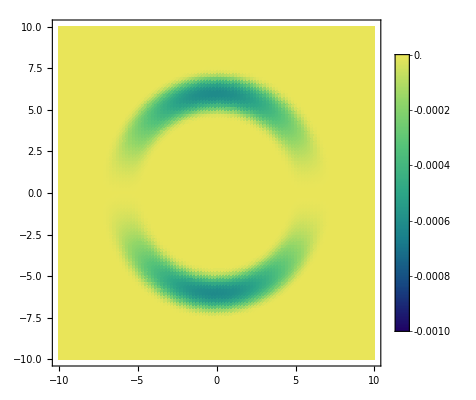

```mathematica
ClearAll[ρ];
ρ=y/Sqrt[y^2+z^2];

ClearAll[f];
f=FullSimplify[TopHat[σ,R,r],{σ∈Reals,R∈Reals,x∈Reals,σ>0,R>0,r>=0}];

ClearAll[r];
r=Sqrt[(x-v*t)^2+y^2+z^2];

ClearAll[vx,vy,vz];
vx[t_,x_,y_,z_]=v*f;
vy[t_,x_,y_,z_]=k*ρ*f;
vz[t_,x_,y_,z_]=0;

ClearAll[σ,R,k,v];
σ=4;
R=4;
k=1/100;
v=1/2;

ClearAll[slice];
slice=Simplify[EnergyDensity//.{t->0,z->0},{x∈Reals,y∈Reals}];

ClearAll[xyRange,zRange];
xyRange=R+σ+2;
zRange={-1/1000,0};

DensityPlot[
slice,
{x,-xyRange,xyRange},
{y,-xyRange,xyRange},

PlotPoints->100,

ColorFunctionScaling->False,
ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,zRange]]&),

PlotRange->{Automatic,Automatic,zRange},

PlotLegends->BarLegend[{Automatic,zRange}],

Exclusions->None
]

ClearAll[xyRange,zRange];
ClearAll[slice];
ClearAll[σ,R,k,v];
ClearAll[vx,vy,vz];
ClearAll[r];
ClearAll[f];
ClearAll[ρ];
```